```mathematica
-1/2 u^2-1/2(y-(a u + b)^2)^2/.{a->√δq,b->√(q1-q0)z1+√q0 z0}
```

-u^2/2-1/2 (y-(√q0 z0+√(-q0+q1) z1+u √δq)^2)^2

```mathematica
D[-1/2 u^2-1/2(y-(a u + b)^2)^2,u]
```

-u+2 a (b+a u) (-(b+a u)^2+y)

```mathematica
Solve[2 y (√q0 z0+√(-q0+q1) z1) √δq-2 (√q0 z0+√(-q0+q1) z1)^3 √δq-6 u^2 (√q0 z0+√(-q0+q1) z1) δq^(3/2)-2 u^3 δq^2+u (-1+2 y δq-6 (√q0 z0+√(-q0+q1) z1)^2 δq)==0,u]
```

{{u→-(√q0 z0+√(-q0+q1) z1)/(√δq)-(2^(1/3) (-δq^2+2 y δq^3))/(δq^2 (-108 √q0 z0 δq^(7/2)-108 √(-q0+q1) z1 δq^(7/2)+√(-864 (-δq^2+2 y δq^3)^3+(-108 √q0 z0 δq^(7/2)-108 √(-q0+q1) z1 δq^(7/2))^2))^(1/3))-((-108 √q0 z0 δq^(7/2)-108 √(-q0+q1) z1 δq^(7/2)+√(-864 (-δq^2+2 y δq^3)^3+(-108 √q0 z0 δq^(7/2)-108 √(-q0+q1) z1 δq^(7/2))^2))^(1/3))/(6 2^(1/3) δq^2)},{u→-(√q0 z0+√(-q0+q1) z1)/(√δq)+((1+ⅈ √3) (-δq^2+2 y δq^3))/(2^(2/3) δq^2 (-108 √q0 z0 δq^(7/2)-108 √(-q0+q1) z1 δq^(7/2)+√(-864 (-δq^2+2 y δq^3)^3+(-108 √q0 z0 δq^(7/2)-108 √(-q0+q1) z1 δq^(7/2))^2))^(1/3))+((1-ⅈ √3) (-108 √q0 z0 δq^(7/2)-108 √(-q0+q1) z1 δq^(7/2)+√(-864 (-δq^2+2 y δq^3)^3+(-108 √q0 z0 δq^(7/2)-108 √(-q0+q1) z1 δq^(7/2))^2))^(1/3))/(12 2^(1/3) δq^2)},{u→-(√q0 z0+√(-q0+q1) z1)/(√δq)+((1-ⅈ √3) (-δq^2+2 y δq^3))/(2^(2/3) δq^2 (-108 √q0 z0 δq^(7/2)-108 √(-q0+q1) z1 δq^(7/2)+√(-864 (-δq^2+2 y δq^3)^3+(-108 √q0 z0 δq^(7/2)-108 √(-q0+q1) z1 δq^(7/2))^2))^(1/3))+((1+ⅈ √3) (-108 √q0 z0 δq^(7/2)-108 √(-q0+q1) z1 δq^(7/2)+√(-864 (-δq^2+2 y δq^3)^3+(-108 √q0 z0 δq^(7/2)-108 √(-q0+q1) z1 δq^(7/2))^2))^(1/3))/(12 2^(1/3) δq^2)}}

```mathematica
FullSimplify[-(√q0 z0+√(-q0+q1) z1)/(√δq)-(2^(1/3) (-δq^2+2 y δq^3))/(δq^2 (-108 √q0 z0 δq^(7/2)-108 √(-q0+q1) z1 δq^(7/2)+√(-864 (-δq^2+2 y δq^3)^3+(-108 √q0 z0 δq^(7/2)-108 √(-q0+q1) z1 δq^(7/2))^2))^(1/3))-((-108 √q0 z0 δq^(7/2)-108 √(-q0+q1) z1 δq^(7/2)+√(-864 (-δq^2+2 y δq^3)^3+(-108 √q0 z0 δq^(7/2)-108 √(-q0+q1) z1 δq^(7/2))^2))^(1/3))/(6 2^(1/3) δq^2)==-(√q0 z0+√(-q0+q1) z1)/(√δq)-(2 y δq-1)/(δq 6^(1/3) (-9 √δq(√(q1-q0) z1+√q0 z0) +√((9 √δq(√(q1-q0) z1+√q0 z0) )^2-6 (2 y δq-1)^3))^(1/3))-((-9 √δq(√(q1-q0) z1+√q0 z0)+√(81(√δq(√(q1-q0) z1+√q0 z0) )^2-6 (2 y δq-1)^3))^(1/3))/(6^(2/3) δq),{Assumptions->{δq>0}}]
```

True

```mathematica
FullSimplify[-(√q0 z0+√(-q0+q1) z1)/(√δq)+((1+ⅈ √3) (-δq^2+2 y δq^3))/(2^(2/3) δq^2 (-108 √q0 z0 δq^(7/2)-108 √(-q0+q1) z1 δq^(7/2)+√(-864 (-δq^2+2 y δq^3)^3+(-108 √q0 z0 δq^(7/2)-108 √(-q0+q1) z1 δq^(7/2))^2))^(1/3))+((1-ⅈ √3) (-108 √q0 z0 δq^(7/2)-108 √(-q0+q1) z1 δq^(7/2)+√(-864 (-δq^2+2 y δq^3)^3+(-108 √q0 z0 δq^(7/2)-108 √(-q0+q1) z1 δq^(7/2))^2))^(1/3))/(12 2^(1/3) δq^2)==-(√q0 z0+√(-q0+q1) z1)/(√δq)+(1+ⅈ √3)/2(2 y δq-1)/(δq 6^(1/3) (-9 √δq(√(q1-q0) z1+√q0 z0) +√(81(√δq(√(q1-q0) z1+√q0 z0) )^2-6 (2 y δq-1)^3))^(1/3))+(1-ⅈ √3)/2((-9 √δq(√(q1-q0) z1+√q0 z0)+√(81(√δq(√(q1-q0) z1+√q0 z0) )^2-6 (2 y δq-1)^3))^(1/3))/(6^(2/3) δq),{Assumptions->{δq>0}}]
```

True

```mathematica
FullSimplify[-(√q0 z0+√(-q0+q1) z1)/(√δq)+((1-ⅈ √3) (-δq^2+2 y δq^3))/(2^(2/3) δq^2 (-108 √q0 z0 δq^(7/2)-108 √(-q0+q1) z1 δq^(7/2)+√(-864 (-δq^2+2 y δq^3)^3+(-108 √q0 z0 δq^(7/2)-108 √(-q0+q1) z1 δq^(7/2))^2))^(1/3))+((1+ⅈ √3) (-108 √q0 z0 δq^(7/2)-108 √(-q0+q1) z1 δq^(7/2)+√(-864 (-δq^2+2 y δq^3)^3+(-108 √q0 z0 δq^(7/2)-108 √(-q0+q1) z1 δq^(7/2))^2))^(1/3))/(12 2^(1/3) δq^2)==-(√q0 z0+√(-q0+q1) z1)/(√δq)+(1-ⅈ √3)/2(2 y δq-1)/(δq 6^(1/3) (-9 √δq(√(q1-q0) z1+√q0 z0) +√(81(√δq(√(q1-q0) z1+√q0 z0) )^2-6 (2 y δq-1)^3))^(1/3))+(1+ⅈ √3)/2((-9 √δq(√(q1-q0) z1+√q0 z0)+√(81(√δq(√(q1-q0) z1+√q0 z0) )^2-6 (2 y δq-1)^3))^(1/3))/(6^(2/3) δq),{Assumptions->{δq>0}}]
```

True

```mathematica
Manipulate[{Plot[{-u^2/2-1/2 (y-(√q0 z0+√(-q0+q1) z1+u √δq)^2)^2},{u,-20,20},PlotRange->{-100,100},GridLines->{{-(√q0 z0+√(-q0+q1) z1)/(√δq)-(2 y δq-1)/(δq 6^(1/3) (-9 √δq(√(q1-q0) z1+√q0 z0) +√((9 √δq(√(q1-q0) z1+√q0 z0) )^2-6 (2 y δq-1)^3))^(1/3))-((-9 √δq(√(q1-q0) z1+√q0 z0)+√(81(√δq(√(q1-q0) z1+√q0 z0) )^2-6 (2 y δq-1)^3))^(1/3))/(6^(2/3) δq),Re[-(√q0 z0+√(-q0+q1) z1)/(√δq)+(1+ⅈ √3)/2(2 y δq-1)/(δq 6^(1/3) (-9 √δq(√(q1-q0) z1+√q0 z0) +√(81(√δq(√(q1-q0) z1+√q0 z0) )^2-6 (2 y δq-1)^3))^(1/3))+(1-ⅈ √3)/2((-9 √δq(√(q1-q0) z1+√q0 z0)+√(81(√δq(√(q1-q0) z1+√q0 z0) )^2-6 (2 y δq-1)^3))^(1/3))/(6^(2/3) δq)],Re[-(√q0 z0+√(-q0+q1) z1)/(√δq)+(1-ⅈ √3)/2(2 y δq-1)/(δq 6^(1/3) (-9 √δq(√(q1-q0) z1+√q0 z0) +√(81(√δq(√(q1-q0) z1+√q0 z0) )^2-6 (2 y δq-1)^3))^(1/3))+(1+ⅈ √3)/2((-9 √δq(√(q1-q0) z1+√q0 z0)+√(81(√δq(√(q1-q0) z1+√q0 z0) )^2-6 (2 y δq-1)^3))^(1/3))/(6^(2/3) δq)]}}],-(√q0 z0+√(-q0+q1) z1)/(√δq)-(2 y δq-1)/(δq 6^(1/3) (-9 √δq(√(q1-q0) z1+√q0 z0) +√((9 √δq(√(q1-q0) z1+√q0 z0) )^2-6 (2 y δq-1)^3))^(1/3))-((-9 √δq(√(q1-q0) z1+√q0 z0)+√(81(√δq(√(q1-q0) z1+√q0 z0) )^2-6 (2 y δq-1)^3))^(1/3))/(6^(2/3) δq),Re[-(√q0 z0+√(-q0+q1) z1)/(√δq)+(1+ⅈ √3)/2(2 y δq-1)/(δq 6^(1/3) (-9 √δq(√(q1-q0) z1+√q0 z0) +√(81(√δq(√(q1-q0) z1+√q0 z0) )^2-6 (2 y δq-1)^3))^(1/3))+(1-ⅈ √3)/2((-9 √δq(√(q1-q0) z1+√q0 z0)+√(81(√δq(√(q1-q0) z1+√q0 z0) )^2-6 (2 y δq-1)^3))^(1/3))/(6^(2/3) δq)],Re[-(√q0 z0+√(-q0+q1) z1)/(√δq)+(1-ⅈ √3)/2(2 y δq-1)/(δq 6^(1/3) (-9 √δq(√(q1-q0) z1+√q0 z0) +√(81(√δq(√(q1-q0) z1+√q0 z0) )^2-6 (2 y δq-1)^3))^(1/3))+(1+ⅈ √3)/2((-9 √δq(√(q1-q0) z1+√q0 z0)+√(81(√δq(√(q1-q0) z1+√q0 z0) )^2-6 (2 y δq-1)^3))^(1/3))/(6^(2/3) δq)]},{q0,0,0.4},{q1,0.41,0.8},{δq,0,5},{y,0.2,5},{z0,-5,5},{z1,-5,5}]
```

```mathematica
-u^2/2-1/2 (y-(√q0 z0+√(-q0+q1) z1+u √δq)^2)^2/.{u->-(√q0 z0+√(-q0+q1) z1)/(√δq)-(2 y δq-1)/(δq 6^(1/3) (-9 √δq(√(q1-q0) z1+√q0 z0) +√((9 √δq(√(q1-q0) z1+√q0 z0) )^2-6 (2 y δq-1)^3))^(1/3))-((-9 √δq(√(q1-q0) z1+√q0 z0)+√(81(√δq(√(q1-q0) z1+√q0 z0) )^2-6 (2 y δq-1)^3))^(1/3))/(6^(2/3) δq) }
```

```mathematica
Solve[-1/2 (-(√q0 z0+√(-q0+q1) z1)/(√δq)-(-1+2 y δq)/(6^(1/3) δq (-9 (√q0 z0+√(-q0+q1) z1) √δq+√(81 (√q0 z0+√(-q0+q1) z1)^2 δq-6 (-1+2 y δq)^3))^(1/3))-((-9 (√q0 z0+√(-q0+q1) z1) √δq+√(81 (√q0 z0+√(-q0+q1) z1)^2 δq-6 (-1+2 y δq)^3))^(1/3))/(6^(2/3) δq))^2-1/2 (y-(√q0 z0+√(-q0+q1) z1+√δq (-(√q0 z0+√(-q0+q1) z1)/(√δq)-(-1+2 y δq)/(6^(1/3) δq (-9 (√q0 z0+√(-q0+q1) z1) √δq+√(81 (√q0 z0+√(-q0+q1) z1)^2 δq-6 (-1+2 y δq)^3))^(1/3))-((-9 (√q0 z0+√(-q0+q1) z1) √δq+√(81 (√q0 z0+√(-q0+q1) z1)^2 δq-6 (-1+2 y δq)^3))^(1/3))/(6^(2/3) δq)))^2)^2==0,z1]
```

```mathematica
-u^2/2-1/2 (y-(a+u √δq)^2)^2/.{u->-a/(√δq)-(2 y δq-1)/(δq 6^(1/3) (-9 √δq(a) +√((9 √δq(a) )^2-6 (2 y δq-1)^3))^(1/3))-((-9 √δq(a)+√(81(√δq(a) )^2-6 (2 y δq-1)^3))^(1/3))/(6^(2/3) δq) }
```

```mathematica
-u^2/2-1/2 (y-(a+u √δq)^2)^2/.{u->-a/(√δq)+(1-ⅈ √3)/2(2 y δq-1)/(δq 6^(1/3) (-9 √δq(a) +√(81(√δq(a) )^2-6 (2 y δq-1)^3))^(1/3))+(1+ⅈ √3)/2((-9 √δq(a)+√(81(√δq(a) )^2-6 (2 y δq-1)^3))^(1/3))/(6^(2/3) δq) }
```

-1/2 (-a/(√δq)+((1-ⅈ √3) (-1+2 y δq))/(2 6^(1/3) δq (-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))+((1+ⅈ √3) (-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))/(2 6^(2/3) δq))^2-1/2 (y-(a+√δq (-a/(√δq)+((1-ⅈ √3) (-1+2 y δq))/(2 6^(1/3) δq (-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))+((1+ⅈ √3) (-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))/(2 6^(2/3) δq)))^2)^2

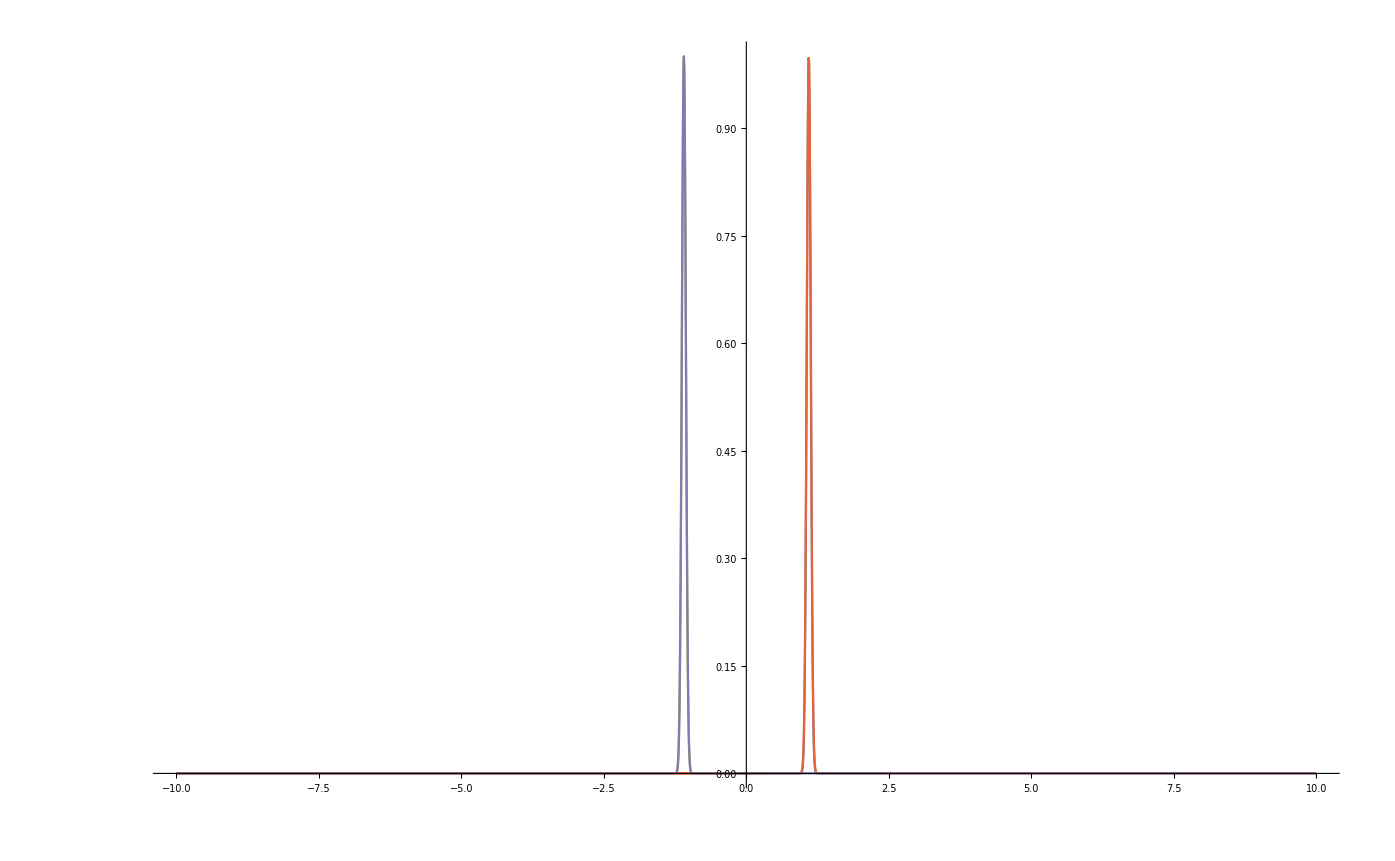

```mathematica
With[{δq=1.,y=1.2,m=1000},Plot[{Exp[-m/2 (-a/(√δq)+((1+ⅈ √3) (-1+2 y δq))/(2 6^(1/3) δq (-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))+((1-ⅈ √3) (-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))/(2 6^(2/3) δq))^2-m/2 (y-(a+√δq (-a/(√δq)+((1+ⅈ √3) (-1+2 y δq))/(2 6^(1/3) δq (-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))+((1-ⅈ √3) (-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))/(2 6^(2/3) δq)))^2)^2],Exp[-m/2 (-a/(√δq)+((1-ⅈ √3) (-1+2 y δq))/(2 6^(1/3) δq (-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))+((1+ⅈ √3) (-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))/(2 6^(2/3) δq))^2-m/2 (y-(a+√δq (-a/(√δq)+((1-ⅈ √3) (-1+2 y δq))/(2 6^(1/3) δq (-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))+((1+ⅈ √3) (-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))/(2 6^(2/3) δq)))^2)^2],Exp[-m/2 (a/(√δq)+(-1+2 y δq)/(6^(1/3) δq (-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))+((-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))/(6^(2/3) δq))^2-m/2 (y-( (-1+2 y δq)/(6^(1/3) √δq (-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))+((-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))/(6^(2/3) √δq))^2)^2], Exp[ -m(a-√y)^2/(2δq +0.5 y)],Exp[-m(a+√y)^2/(2δq+0.5y )]},{a,-10,10}, PlotRange->All]]
```

```mathematica
Series[-m/2 (a/(√δq)+(-1+2 y δq)/(6^(1/3) δq (-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))+((-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))/(6^(2/3) δq))^2-m/2 (y-( (-1+2 y δq)/(6^(1/3) √δq (-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))+((-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))/(6^(2/3) √δq))^2)^2,{a,0,2}]
```

-(m (-2+8 y δq+4 y^2 δq^2+(-(-1+2 y δq)^3)^(1/3)-2 y δq (-(-1+2 y δq)^3)^(1/3)+(-(-1+2 y δq)^3)^(2/3)))/(24 δq^2)+(m (-(-(-1+2 y δq)^3)^(1/6)+4 y δq (-(-1+2 y δq)^3)^(1/6)-4 y^2 δq^2 (-(-1+2 y δq)^3)^(1/6)+(-(-1+2 y δq)^3)^(5/6)) a)/(√6 δq^(3/2) (-1+2 y δq)^2)-((m (-2+12 y δq-24 y^2 δq^2+16 y^3 δq^3+(-(-1+2 y δq)^3)^(1/3)-2 y δq (-(-1+2 y δq)^3)^(1/3)+(-(-1+2 y δq)^3)^(2/3))) a^2)/(4 (δq (-1+2 y δq)^3))+O[a]^3

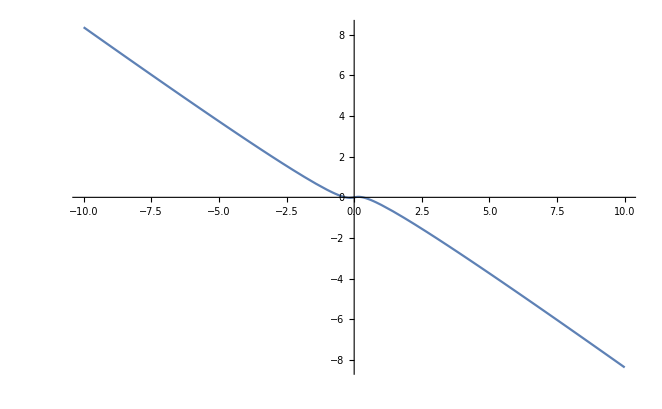

```mathematica
With[{δq=1,y=0.1},Plot[- (1/(√δq)-((-1+2 y δq) (-9 √δq+(81 a δq)/(√(81 a^2 δq-6 (-1+2 y δq)^3))))/(3 6^(1/3) δq (-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(4/3))+(-9 √δq+(81 a δq)/(√(81 a^2 δq-6 (-1+2 y δq)^3)))/(3 6^(2/3) δq (-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(2/3))) (a/(√δq)+(-1+2 y δq)/(6^(1/3) δq (-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))+((-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))/(6^(2/3) δq))+2 (-((-1+2 y δq) (-9 √δq+(81 a δq)/(√(81 a^2 δq-6 (-1+2 y δq)^3))))/(3 6^(1/3) √δq (-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(4/3))+(-9 √δq+(81 a δq)/(√(81 a^2 δq-6 (-1+2 y δq)^3)))/(3 6^(2/3) √δq (-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(2/3))) ((-1+2 y δq)/(6^(1/3) √δq (-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))+((-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))/(6^(2/3) √δq)) (y-((-1+2 y δq)/(6^(1/3) √δq (-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))+((-9 a √δq+√(81 a^2 δq-6 (-1+2 y δq)^3))^(1/3))/(6^(2/3) √δq))^2),{a,-10,10}]]
```

## Finite Temperature

```mathematica
-1/2 u^2-β/2(y-(a u + b)^2)^2/.{a->√(1-q1),b->√(q1-q0)z1+√q0 z0}
```

-u^2/2-1/2 (y-(√(1-q1) u+√q0 z0+√(-q0+q1) z1)^2)^2 β

```mathematica
D[-u^2/2-1/2 (y-(√δq u+√q0 z0+√(-q0+q1) z1)^2)^2 β,u]
```

-u+2 β (y-(√q0 z0+√(-q0+q1) z1+u √δq)^2) (√q0 z0+√(-q0+q1) z1+u √δq) √δq

```mathematica
Solve[-u+2 β (y-(√q0 z0+√(-q0+q1) z1+u √δq)^2) (√q0 z0+√(-q0+q1) z1+u √δq) √δq==0, u]
```

{{u→-(√q0 z0 β δq^(3/2)+√(-q0+q1) z1 β δq^(3/2))/(β δq^2)-(2^(1/3) (-β δq^2+2 y β^2 δq^3))/(β δq^2 (-108 √q0 z0 β^2 δq^(7/2)-108 √(-q0+q1) z1 β^2 δq^(7/2)+√(-864 (-β δq^2+2 y β^2 δq^3)^3+(-108 √q0 z0 β^2 δq^(7/2)-108 √(-q0+q1) z1 β^2 δq^(7/2))^2))^(1/3))-((-108 √q0 z0 β^2 δq^(7/2)-108 √(-q0+q1) z1 β^2 δq^(7/2)+√(-864 (-β δq^2+2 y β^2 δq^3)^3+(-108 √q0 z0 β^2 δq^(7/2)-108 √(-q0+q1) z1 β^2 δq^(7/2))^2))^(1/3))/(6 2^(1/3) β δq^2)},{u→-(√q0 z0 β δq^(3/2)+√(-q0+q1) z1 β δq^(3/2))/(β δq^2)+((1+ⅈ √3) (-β δq^2+2 y β^2 δq^3))/(2^(2/3) β δq^2 (-108 √q0 z0 β^2 δq^(7/2)-108 √(-q0+q1) z1 β^2 δq^(7/2)+√(-864 (-β δq^2+2 y β^2 δq^3)^3+(-108 √q0 z0 β^2 δq^(7/2)-108 √(-q0+q1) z1 β^2 δq^(7/2))^2))^(1/3))+((1-ⅈ √3) (-108 √q0 z0 β^2 δq^(7/2)-108 √(-q0+q1) z1 β^2 δq^(7/2)+√(-864 (-β δq^2+2 y β^2 δq^3)^3+(-108 √q0 z0 β^2 δq^(7/2)-108 √(-q0+q1) z1 β^2 δq^(7/2))^2))^(1/3))/(12 2^(1/3) β δq^2)},{u→-(√q0 z0 β δq^(3/2)+√(-q0+q1) z1 β δq^(3/2))/(β δq^2)+((1-ⅈ √3) (-β δq^2+2 y β^2 δq^3))/(2^(2/3) β δq^2 (-108 √q0 z0 β^2 δq^(7/2)-108 √(-q0+q1) z1 β^2 δq^(7/2)+√(-864 (-β δq^2+2 y β^2 δq^3)^3+(-108 √q0 z0 β^2 δq^(7/2)-108 √(-q0+q1) z1 β^2 δq^(7/2))^2))^(1/3))+((1+ⅈ √3) (-108 √q0 z0 β^2 δq^(7/2)-108 √(-q0+q1) z1 β^2 δq^(7/2)+√(-864 (-β δq^2+2 y β^2 δq^3)^3+(-108 √q0 z0 β^2 δq^(7/2)-108 √(-q0+q1) z1 β^2 δq^(7/2))^2))^(1/3))/(12 2^(1/3) β δq^2)}}

```mathematica
FullSimplify[-(√q0 z0 β δq^(3/2)+√(-q0+q1) z1 β δq^(3/2))/(β δq^2)-(2^(1/3) (-β δq^2+2 y β^2 δq^3))/(β δq^2 (-108 √q0 z0 β^2 δq^(7/2)-108 √(-q0+q1) z1 β^2 δq^(7/2)+√(-864 (-β δq^2+2 y β^2 δq^3)^3+(-108 √q0 z0 β^2 δq^(7/2)-108 √(-q0+q1) z1 β^2 δq^(7/2))^2))^(1/3))-((-108 √q0 z0 β^2 δq^(7/2)-108 √(-q0+q1) z1 β^2 δq^(7/2)+√(-864 (-β δq^2+2 y β^2 δq^3)^3+(-108 √q0 z0 β^2 δq^(7/2)-108 √(-q0+q1) z1 β^2 δq^(7/2))^2))^(1/3))/(6 2^(1/3) β δq^2)==-(√q0 z0 +√(-q0+q1) z1)/(√δq)-(2 y β δq-1)/(6^(1/3)δq(-9 β^2 √δq( √q0 z0 + √(q1-q0) z1) +√((9 β^2 √δq( √q0 z0 + √(q1-q0) z1))^2-6 β^3(2 y β δq-1)^3))^(1/3))-((-9 β^2 √δq( √q0 z0 + √(q1-q0) z1) +√((9 β^2 √δq( √q0 z0 + √(q1-q0) z1))^2-6 β^3(2 y β δq-1)^3))^(1/3))/(6^(2/3) δq β),{Assumptions->{δq>0,β>0}}]
```

True

```mathematica
FullSimplify[-(√q0 z0 β δq^(3/2)+√(-q0+q1) z1 β δq^(3/2))/(β δq^2)+((1+ⅈ √3) (-β δq^2+2 y β^2 δq^3))/(2^(2/3) β δq^2 (-108 √q0 z0 β^2 δq^(7/2)-108 √(-q0+q1) z1 β^2 δq^(7/2)+√(-864 (-β δq^2+2 y β^2 δq^3)^3+(-108 √q0 z0 β^2 δq^(7/2)-108 √(-q0+q1) z1 β^2 δq^(7/2))^2))^(1/3))+((1-ⅈ √3) (-108 √q0 z0 β^2 δq^(7/2)-108 √(-q0+q1) z1 β^2 δq^(7/2)+√(-864 (-β δq^2+2 y β^2 δq^3)^3+(-108 √q0 z0 β^2 δq^(7/2)-108 √(-q0+q1) z1 β^2 δq^(7/2))^2))^(1/3))/(12 2^(1/3) β δq^2)==-(√q0 z0 +√(-q0+q1) z1)/(√δq)+(1+ⅈ √3)/2(β (2 y β δq-1))/(6^(1/3)δq β(-9 β^2 √δq( √q0 z0 + √(q1-q0) z1) +√((9 β^2 √δq( √q0 z0 + √(q1-q0) z1))^2-6 β^3(2 y β δq-1)^3))^(1/3))+(1-ⅈ √3)/2((-9 β^2 √δq( √q0 z0 + √(q1-q0) z1) +√((9 β^2 √δq( √q0 z0 + √(q1-q0) z1))^2-6 β^3(2 y β δq-1)^3))^(1/3))/(6^(2/3) δq β),{Assumptions->{δq>0,β>0}}]
```

True

```mathematica
FullSimplify[-(√q0 z0 β δq^(3/2)+√(-q0+q1) z1 β δq^(3/2))/(β δq^2)+((1-ⅈ √3) (-β δq^2+2 y β^2 δq^3))/(2^(2/3) β δq^2 (-108 √q0 z0 β^2 δq^(7/2)-108 √(-q0+q1) z1 β^2 δq^(7/2)+√(-864 (-β δq^2+2 y β^2 δq^3)^3+(-108 √q0 z0 β^2 δq^(7/2)-108 √(-q0+q1) z1 β^2 δq^(7/2))^2))^(1/3))+((1+ⅈ √3) (-108 √q0 z0 β^2 δq^(7/2)-108 √(-q0+q1) z1 β^2 δq^(7/2)+√(-864 (-β δq^2+2 y β^2 δq^3)^3+(-108 √q0 z0 β^2 δq^(7/2)-108 √(-q0+q1) z1 β^2 δq^(7/2))^2))^(1/3))/(12 2^(1/3) β δq^2)==-(√q0 z0 +√(-q0+q1) z1)/(√δq)+(1-ⅈ √3)/2(β(2 y β δq-1))/(6^(1/3)δq β(-9 β^2 √δq( √q0 z0 + √(q1-q0) z1) +√((9 β^2 √δq( √q0 z0 + √(q1-q0) z1))^2-6 β^3(2 y β δq-1)^3))^(1/3))+(1+ⅈ √3)/2((-9 β^2 √δq( √q0 z0 + √(q1-q0) z1) +√((9 β^2 √δq( √q0 z0 + √(q1-q0) z1))^2-6 β^3(2 y β δq-1)^3))^(1/3))/(6^(2/3) δq β),{Assumptions->{δq>0,β>0}}]
```

True

```mathematica
Gs[m_,qh0_,qh1_,qh2_,ph_]:=0.5*((qh0+ph^2)/(qh1-qh2+m*(qh0-qh1))+(1-m)/m*Log[qh1-qh2]-1/m*Log[qh1-qh2+m*(qh0-qh1)])
```

```mathematica
D[Gs[m,qh0,qh1,qh2,ph], m]
```

0.5 (-((ph^2+qh0) (qh0-qh1))/(m (qh0-qh1)+qh1-qh2)^2-(qh0-qh1)/(m (m (qh0-qh1)+qh1-qh2))-((1-m) Log[qh1-qh2])/m^2-Log[qh1-qh2]/m+Log[m (qh0-qh1)+qh1-qh2]/m^2)

```mathematica
Simplify[(-((ph^2+qh0) (qh0-qh1))/(m (qh0-qh1)+qh1-qh2)^2-(qh0-qh1)/(m (m (qh0-qh1)+qh1-qh2))-((1-m) Log[qh1-qh2])/m^2-Log[qh1-qh2]/m+Log[m (qh0-qh1)+qh1-qh2]/m^2)==((qh1-qh0)/(m (qh0-qh1)+qh1-qh2)((ph^2+qh0)/(m (qh0-qh1)+qh1-qh2)+1/m)+1/m^2 (Log[m (qh0-qh1)+qh1-qh2]-Log[qh1-qh2]))]
```

True

```mathematica
Series[-(q0*z0^2+y)/(2(1-q0))-0.5*Log[2π*y*(1-q0)]+Log[Cosh[√(y*q0)*z0/(1-q0)]]/.{q0-> 1-dq},{dq,0,2}]
```

Log[Cosh[(√((1-dq) y) z0)/dq]]+((-y/2-z0^2/2)/dq+0.5 (z0^2-1. Log[dq]-1. Log[2 π y])+O[dq]^3)

```mathematica
-(q0*z0^2+y)/(2(1-q0))-0.5*Log[2π*y*(1-q0)]+Log[Cosh[√(y*q0)*z0/(1-q0)]]/.{q0-> 1-dq}
```

(-y-(1-dq) z0^2)/(2 dq)-0.5 Log[2 dq π y]+Log[Cosh[(√((1-dq) y) z0)/dq]]

```mathematica
With[{q0=1-0.000001,z0=.01,y=.01},{-Log[2]+1/(1-q0)(√(q0 y)Abs[z0]-y/2-z0^2/2)+1/2(z0^2-Log[1-q0]-Log[2 π y]),-(q0*z0^2+y)/(2(1-q0))-0.5*Log[2π*y*(1-q0)]+Log[Cosh[√(y*q0)*z0/(1-q0)]]}
]
```

{-4042.4,-4042.4}

```mathematica
-Log[2]+1/(1-q0)(√(q0 y)Abs[z0]-y/2-z0^2/2)+1/2(z0^2-Log[1-q0]-Log[2 π y])/.{q0-> 1-dq}
```

(-y/2-z0^2/2+√((1-dq) y) Abs[z0])/dq-Log[2]+1/2 (z0^2-Log[dq]-Log[2 π y])

```mathematica
D[-(q0*z0^2+y)/(2(1-q0))-0.5*Log[2π*y*(1-q0)]+Log[Cosh[√(y*q0)*z0/(1-q0)]],q0]
```

0.5/(1-q0)-z0^2/(2 (1-q0))+(-y-q0 z0^2)/(2 (1-q0)^2)+((y z0)/(2 (1-q0) √(q0 y))+(√(q0 y) z0)/(1-q0)^2) Tanh[(√(q0 y) z0)/(1-q0)]

```mathematica
0.5/(1-q0)-z0^2/(2 (1-q0))+(-y-q0 z0^2)/(2 (1-q0)^2)+((y z0)/(2 (1-q0) √(q0 y))+(√(q0 y) z0)/(1-q0)^2) Tanh[(√(q0 y) z0)/(1-q0)]
```

```mathematica
D[-(q0*z0^2+y)/(2(1-q0))-0.5*Log[2π*y*(1-q0)]+Log[Cosh[√(y*q0)*z0/(1-q0)]],y]
```

-1/(2 (1-q0))-0.5/y+(q0 z0 Tanh[(√(q0 y) z0)/(1-q0)])/(2 (1-q0) √(q0 y))

```mathematica
-1/(2 (1-q0))-0.5/y+(q0 z0 Tanh[(√(q0 y) z0)/(1-q0)])/(2 (1-q0) √(q0 y))
```

```mathematica
D[(√(1-q0)*u0+√q0*z0)^2,q0]
```

2 (-u0/(2 √(1-q0))+z0/(2 √q0)) (√(1-q0) u0+√q0 z0)

```mathematica
Expand[(-1/(1-q0)-1/y+(q0 z0 Tanh[(√(q0 y) z0)/(1-q0)])/((1-q0) √(q0 y))) (-u0/(2 √(1-q0))+z0/(2 √q0)) (√(1-q0) u0+√q0 z0)]
```

u0^2/(2 (1-q0))+u0^2/(2 y)-(u0 z0)/(2 √(1-q0) √q0)+(√q0 u0 z0)/(2 (1-q0)^(3/2))-(√(1-q0) u0 z0)/(2 √q0 y)+(√q0 u0 z0)/(2 √(1-q0) y)-z0^2/(2 (1-q0))-z0^2/(2 y)-(u0^2 √(q0 y) z0 Tanh[(√(q0 y) z0)/(1-q0)])/(2 (1-q0) y)+(u0 √(q0 y) z0^2 Tanh[(√(q0 y) z0)/(1-q0)])/(2 √(1-q0) √q0 y)-(√q0 u0 √(q0 y) z0^2 Tanh[(√(q0 y) z0)/(1-q0)])/(2 (1-q0)^(3/2) y)+(√(q0 y) z0^3 Tanh[(√(q0 y) z0)/(1-q0)])/(2 (1-q0) y)

```mathematica
-(q0*z0^2+y)/(2(1-q0))-0.5*Log[2π*y*(1-q0)]+Log[Cosh[√(y*q0)*z0/(1-q0)]]/.{y-> (√(1-q0)*u0+√q0*z0)^2}
```

```mathematica
D[(-q0 z0^2-(√(1-q0) u0+√q0 z0)^2)/(2 (1-q0))-0.5 Log[2 π (1-q0) (√(1-q0) u0+√q0 z0)^2]+Log[Cosh[(z0 √(q0 (√(1-q0) u0+√q0 z0)^2))/(1-q0)]],q0]
```

```mathematica
(-z0^2-2 (-u0/(2 √(1-q0))+z0/(2 √q0)) √y)/(2 (1-q0))+(-q0 z0^2-y)/(2 (1-q0)^2)-(2 (1-q0) (-u0/(2 √(1-q0))+z0/(2 √q0)) √y- y)/(2(1-q0) y)+((z0 √(q0 y))/(1-q0)^2+(z0 (2 q0 (-u0/(2 √(1-q0))+z0/(2 √q0)) √y+y))/(2 (1-q0) √(q0 y))) Tanh[(z0 √(q0 y))/(1-q0)]
```

```mathematica
Simplify[1/2 (1/(1-q0)-(y+z0^2)/(1-q0)^2+(1/(√y)+(√y)/(1-q0) )(u0/(√(1-q0))-z0/(√q0))+(2z0  √(q0 y) Tanh[(√(q0 y) z0)/(1-q0)])/(1-q0)^2+(z0 (y+√(q0 y) z0-(q0 u0 √y)/(√(1-q0))) Tanh[(√(q0 y) z0)/(1-q0)])/((1-q0) √(q0 y)))==0.5/(1-q0)-z0^2/(2 (1-q0))+(-y-q0 z0^2)/(2 (1-q0)^2)+((y z0)/(2 (1-q0) √(q0 y))+(√(q0 y) z0)/(1-q0)^2) Tanh[(√(q0 y) z0)/(1-q0)]+(-1/(2 (1-q0))-0.5/y+(q0 z0 Tanh[(√(q0 y) z0)/(1-q0)])/(2 (1-q0) √(q0 y)))2 (-u0/(2 √(1-q0))+z0/(2 √q0)) √y,Assumptions->{y>0,q0>0}]
```

True

```mathematica
0.07957747154594767 *4π
```

1.

```mathematica
Simplify[+1/(2(1-q0))-z0^2/(2(1-q0)^2)-((-u0/(2 √(1-q0))+z0/(2 √q0)) √y)/(1-q0)-y/(2 (1-q0)^2)-(-u0/(2 √(1-q0))+z0/(2 √q0))/(√y)+((z0 √(q0 y))/(1-q0)^2+(z0 (2 q0 (-u0/(2 √(1-q0))+z0/(2 √q0)) √y+y))/(2 (1-q0) √(q0 y))) Tanh[(z0 √(q0 y))/(1-q0)]]
```

1/2 (1/(1-q0)-y/(-1+q0)^2-z0^2/(-1+q0)^2+(u0/(√(1-q0))-z0/(√q0))/(√y)+√y (u0/(1-q0)^(3/2)+z0/((-1+q0) √q0))+(z0 (2 q0 y+(1-q0) (-(q0 u0 √y)/(√(1-q0))+y+√q0 √y z0)) Tanh[(√(q0 y) z0)/(1-q0)])/((-1+q0)^2 √(q0 y)))

```mathematica
CForm[1/2 (1/(1-q0)-(y+z0^2)/(1-q0)^2+(1/(√y)+(√y)/(1-q0) )(u0/(√(1-q0))-z0/(√q0))+(2z0  √(q0 y) Tanh[(√(q0 y) z0)/(1-q0)])/(1-q0)^2+(z0 (y+√(q0 y) z0-(q0 u0 √y)/(√(1-q0))) Tanh[(√(q0 y) z0)/(1-q0)])/((1-q0) √(q0 y)))]
```

(1/(1 - q0) + (1/Sqrt(y) + Sqrt(y)/(1 - q0))*(u0/Sqrt(1 - q0) - z0/Sqrt(q0)) - (y + Power(z0,2))/Power(1 - q0,2) + (2*Sqrt(q0*y)*z0*Tanh((Sqrt(q0*y)*z0)/(1 - q0)))/Power(1 - q0,2) + 
     (z0*(-((q0*u0*Sqrt(y))/Sqrt(1 - q0)) + y + Sqrt(q0*y)*z0)*Tanh((Sqrt(q0*y)*z0)/(1 - q0)))/((1 - q0)*Sqrt(q0*y)))/2.